```mathematica
(* Below I'll use t for the variable and x and y for the data.  You could use xs and ys for data and x for the variable, but we can't use the symbol x for two different things. *)
```

```mathematica
x:={0.0, 0.5, 1.0}
f[t_]:=Exp[t]
y:=Exp[x]
```

```mathematica
x[[1]]
y[[1]]
```

0.

1.

```mathematica
L0[t_]:=((t-x[[2]])*(t-x[[3]]))/(((x[[1]]-x[[2]])*(x[[1]]-x[[3]])))
L1[t_]:=((t-x[[1]])*(t-x[[3]]))/(((x[[2]]-x[[1]])*(x[[2]]-x[[3]])))
L2[t_]:=((t-x[[1]])*(t-x[[2]]))/(((x[[3]]-x[[1]])*(x[[3]]-x[[2]])))
```

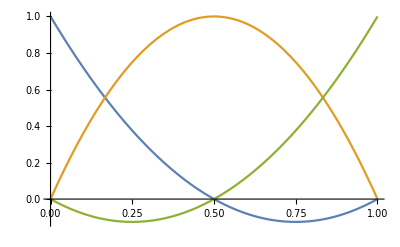

```mathematica
Plot[{L0[t], L1[t],L2[t]},{t,x[[1]], x[[3]]}]
```

```mathematica
P[t_]:=y[[1]]*L0[t]+y[[2]]*L1[t]+y[[3]]*L2[t]
Expand[P[t]]
```

1.+0.876603 t+0.841679 t^2

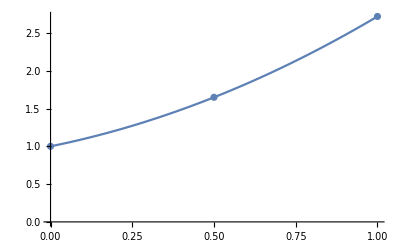

```mathematica
a:=Plot[P[t],{t,x[[1]],x[[3]]}]
b:=ListPlot[Table[{x[[j]],y[[j]]},{j,1,Length[x]}]]
Show[b,a]
```

```mathematica
Table[{x[[j]],y[[j]]},{j,1,Length[x]}]
Table[{x[[j]],f[x[[j]]]},{j,1,Length[x]}]
Table[{x[[j]],f'[x[[j]]]},{j,1,Length[x]}]
```

{{0.,1.},{0.5,1.64872},{1.,2.71828}}

{{0.,1.},{0.5,1.64872},{1.,2.71828}}

{{0.,1.},{0.5,1.64872},{1.,2.71828}}

```mathematica
(* Hermite *)
h0[t_]:= (1-2*(t-x[[1]])*L0'[x[[1]]])*(L0[t])^2
h1[t_]:= (1-2*(t-x[[2]])*L1'[x[[2]]])*(L1[t])^2
h2[t_]:= (1-2*(t-x[[3]])*L2'[x[[3]]])*(L2[t])^2

hh0[t_]:= (t-x[[1]])*(L0[t])^2
hh1[t_]:= (t-x[[2]])*(L1[t])^2
hh2[t_]:= (t-x[[3]])*(L2[t])^2

H[t_]:= f[x[[1]]]*h0[t]+f[x[[2]]]*h1[t]+f[x[[3]]]*h2[t]+f'[x[[1]]]*hh0[t]+f'[x[[2]]]*hh1[t]+f'[x[[3]]]*hh2[t]
Expand[H[t]]
```

1.+1. t+0.499461 t^2+0.169827 t^3+0.03509 t^4+0.0139038 t^5

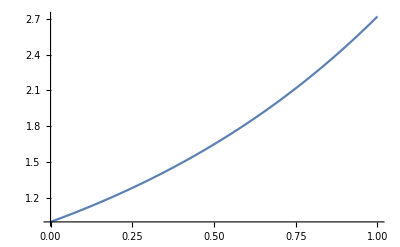

```mathematica
Plot[H[t],{t,0,1}]
```

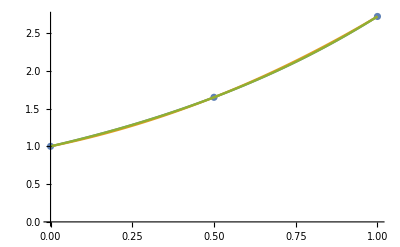

```mathematica
(* Everything *)
a:=Plot[{f[t],P[t],H[t]},{t,x[[1]],x[[Length[x]]]}]
b:=ListPlot[Table[{x[[j]],y[[j]]},{j,1,Length[x]}]]
Show[b,a]
```